```mathematica
ex8 = Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/8_Lab/table/t1.csv"];
```

```mathematica
TableForm[ex8]
```

Frequency (Hz) | Uncertainty (Hz) | V_a | Uncertainty (V_a) | V_b(uV) | Uncertainty(V_b) | Actual | Predicted | Residuals
100.83 | 10 | 0.6605 | 10 | 8.916 | 1 | 13449.5 | 12398.6 | 1050.83
249.8 | 1 | 0.6622 | 10 | 8.92 | 1 | 13420.9 | 12576.6 | 844.386
500.1 | 1 | 0.6642 | 10 | 8.898 | 1 | 13347.5 | 12875.5 | 472.011
750.3 | 1 | 0.6644 | 10 | 8.907 | 1 | 13357. | 13174.4 | 182.649
1000 | 1 | 0.6647 | 10 | 8.923 | 10 | 13375. | 13472.6 | -97.6411
5000 | 1 | 0.6674 | 10 | 4.59 | 10 | 6852.26 | 18250.3 | -11398.
20140 | 1 | 0.662 | 10 | 18.08 | 1 | 27211.2 | 36333.6 | -9122.4
40280 | 1 | 0.6611 | 10 | 36.28 | 1 | 54677.4 | 60389. | -5711.66
59740 | 1 | 0.6581 | 10 | 54.01 | 1 | 81769.2 | 83632.3 | -1863.03
79200 | 1 | 0.657 | 10 | 72.18 | 1 | 109461. | 106875. | 2585.44
99660 | 1 | 0.6551 | 10 | 88.48 | 1 | 134569. | 131313. | 3255.92

```mathematica
col1 = ex8[[All, 1]][[2 ;; 12]];
col2 = ex8[[All, 2]][[2 ;; 12]];
col3 = ex8[[All, 3]][[2 ;; 12]];
col4 = ex8[[All, 4]][[2 ;; 12]];
col5 = ex8[[All, 5]][[2 ;; 12]];
col6 = ex8[[All, 6]][[2 ;; 12]];
col7 = ex8[[All, 7]][[2 ;; 12]];
col8 = ex8[[All, 8]][[2 ;; 12]];
col9 = ex8[[All, 9]][[2 ;; 12]];
```

```mathematica
r1 = 0.99634 * 1000; (*resistor-1*)
col7 = col5 / col3;
colR = r1 * col7; (*Resistance*)
colU = col6 / col2; (*Uncertainty*)
```

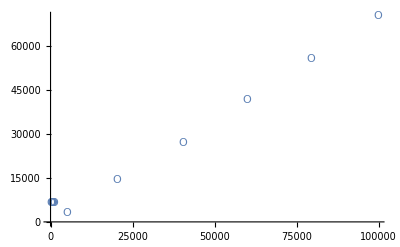

FittedModel[4464.29+0.637334 x]

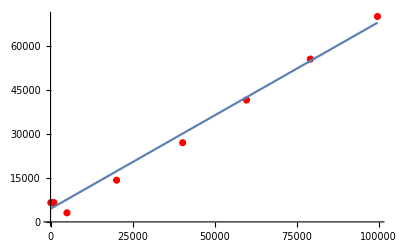
-Graphics-ResistanceFrequency (Hz)

4464.29+0.637334 x

```mathematica
(*Plot Chart*)
ex8Pair = {col1, colR};
ex8Tuple = Transpose[ex8Pair];
ListPlot[ex8Tuple, PlotMarkers->{"O"}]

(**************************************)
(**************************************)
(**************************************)
(**************************************)


(*Weighted Least Square Fit*)
sim=Flatten[MapThread[Function[{a},{#1[[1]],a}]/@RandomVariate[NormalDistribution[#1[[2]],#2],200]&,{ex8Tuple,colU}],1];
fit2=LinearModelFit[ex8Tuple,x,x,Weights->1/colU]
Labeled[
Show[
ListPlot[ex8Tuple,PlotStyle->Red],
Plot[{fit2[x]},{x,0,ex8Tuple[[-1,1]]}]   ],
{"Resistance", "Frequency (Hz)"},
{Left, Bottom},
RotateLabel->True
]
Normal@fit2
```

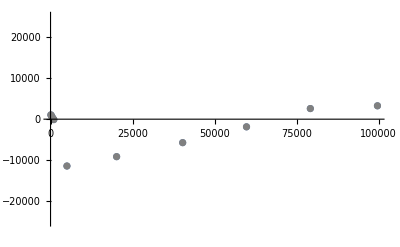
-Graphics-V.b2 (mV).b2R(kΩ)

```mathematica
(**************************************)
(**************************************)
(**************************************)
(**************************************)

(*Residual Graph*)

ex8ErrPair = {col1, col9};
ex8ErrTuple = Transpose[ex8ErrPair];
ex8Err2Trip = {col1, col9, col4};
ex8ErrT2 = Transpose[ex8Err2Trip];

Needs["ErrorBarPlots`"]
Labeled[
	Show[
	ListPlot[ex8ErrTuple, PlotRange->{-25000, 25000}],     (*Note the Range*)
	ErrorListPlot[ex8ErrT2,PlotStyle->Gray]
   ],
{"V.b2 (mV).b2", "R(kΩ)"},
{Left, Bottom},
RotateLabel->True
]
```